## Use this program when you want to calculate estimated error. Between this program and the CalculateQ program, their generateGroundStates functions are defined differently so they won’t mesh. trash code everything is wrong somehow

{{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}}

{{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}}

Numerical Error:

0.03223

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {229.484}. NIntegrate obtained 1366.67 and 0.136613 for the integral and error estimates.

$Aborted

$Aborted

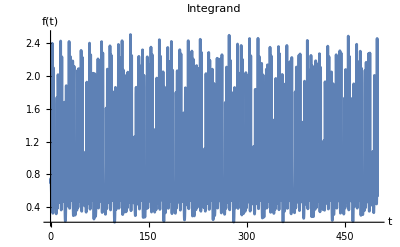

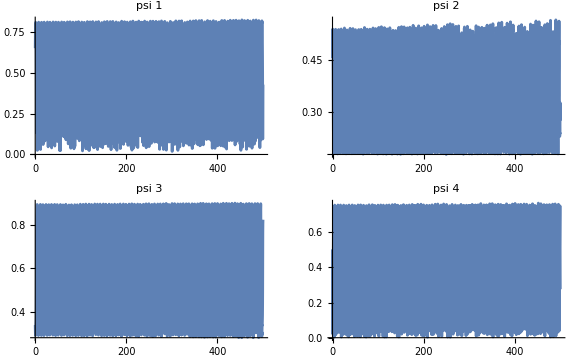

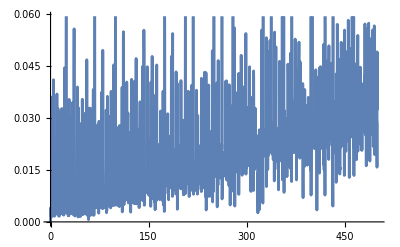

```mathematica
Needs["NumericalCalculus`"]

(*Global Constants*)

initialTime=0;
dimension=4;
t1=1;
t2=1/Sqrt[2];
n=1000;
dt=0.01;


temp=10;
endTime=500;


generateGOEMatrix[n_Integer]:=Module[{matrix},matrix=Table[If[i==j,RandomVariate[NormalDistribution[0,1]],RandomVariate[NormalDistribution[0,1/Sqrt[2]]]],{i,n},{j,n}];
matrix=(matrix+Transpose[matrix])/2;(*Ensure the matrix is symmetric*)matrix]

H[t_]:=Tscale[t]  ((Sin[t/t1] 2.1+Sin[t/t2])*Hinitial+(Cos[t/t1] 2.7+Cos[t/t2])*Hend)



H2[t_] := H[t]/normDerivativeGroundState[t]


groundState[t_]:=Module[{eigenvalues,eigenvectors,minIndex},{eigenvalues,eigenvectors}=Eigensystem[H[t]];
minIndex=First[Ordering[Re[eigenvalues],1]];
Normalize[Re[eigenvectors[[minIndex]]]]]

generateGroundStates[dt_]:=Module[{t,states,currentState,nextState,dotProduct},states={groundState[initialTime]};
currentState=groundState[initialTime];
For[t=initialTime,t<endTime,t+=dt,nextState=groundState[t+dt];
dotProduct=Re[Dot[currentState,nextState]];
If[dotProduct>=0,AppendTo[states,nextState],AppendTo[states,-nextState]];
currentState=Last[states];];
states]

state[t_,n_]:=Module[{eigenvalues,eigenvectors,index},{eigenvalues,eigenvectors}=Eigensystem[H[t]];
index=Ordering[Re[eigenvalues],n+1][[n+1]];
Normalize[Re[eigenvectors[[index]]]]]

generateExcitedStates[dt_,n_]:=Module[{t,states,currentState,nextState,dotProduct},states={state[initialTime,n]};
currentState=state[initialTime,n];
For[t=initialTime,t<endTime,t+=dt,nextState=state[t+dt,n];
dotProduct=Re[Dot[currentState,nextState]];
If[dotProduct>=0,AppendTo[states,nextState],AppendTo[states,-nextState]];
currentState=Last[states];];
states]

(*groundStates=generateGroundStates[0.01];
timeValues=Range[initialTime,endTime,0.01];
plots=Table[ListLinePlot[Transpose[{timeValues,groundStates[[All,i]]}],PlotRange->All,PlotLabel->"Ground State Element "<>ToString[i],AxesLabel->{"t","Element "<>ToString[i]}],{i,Length[groundStates[[1]]]}];
GraphicsGrid[Partition[plots,2]] firstExcitedStates=generateExcitedStates[0.01,2];
timeValues=Range[initialTime,endTime,0.01];
plots=Table[ListLinePlot[Transpose[{timeValues,firstExcitedStates[[All,i]]}],PlotRange->All,PlotLabel->"Excited State Element "<>ToString[i],AxesLabel->{"t","Element "<>ToString[i]}],{i,Length[firstExcitedStates[[1]]]}];
GraphicsGrid[Partition[plots,2]]*)

gap[t_,n_]:=Module[{eigenvalues,sortedEigenvalues,smallestEigenvalue,nEigenvalue,difference},eigenvalues=Re[Eigenvalues[H[t]]];
sortedEigenvalues=Sort[eigenvalues];
smallestEigenvalue=sortedEigenvalues[[1]];
nEigenvalue=sortedEigenvalues[[n+1]];
difference=nEigenvalue-smallestEigenvalue;
difference]


Tscale[t_]:=temp



omega[n_]:=NIntegrate[gap[t,n]/Tscale[t],{t,initialTime,endTime}]


derivativeGroundState[t_?NumericQ,h_:0.01]:=(groundState[t+h]-groundState[t-h]*(groundState[t+h].groundState[t-h]))/(2*h)

normDerivativeGroundState[t_]:=Norm[derivativeGroundState[t]]

Hinitial={{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}}

Hend={{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}}




(*If you don't make it eigenvalues[t] the lines for each eigenvalue are individually colored*)
eigenvalsFunction[t_]:=Eigenvalues[H[t]]


(*groundStateElementsPlots=Table[Plot[groundState[t][[i]],{t,initialTime,endTime},PlotRange->All,PlotLabel->"Ground State Element "<>ToString[i],AxesLabel->{"t","Element "<>ToString[i]}],{i,1,dimension}];
Column[groundStateElementsPlots]*)








(*Plot[Evaluate[Table[eigenvalsFunction[t][[i]],{i,dimension}]],{t,initialTime,endTime},PlotRange->All,PlotLabel->"Eigenvalues",AxesLabel->{"t","E(t)"}]*)






(*
LFunction[t_]:=NIntegrate[normDerivativeGroundState[τ],{τ,initialTime,t},Method->"GlobalAdaptive",MaxRecursion->50,PrecisionGoal->6,AccuracyGoal->6]


Do[Print["LFunction[",i,"] = ",LFunction[i]],{i,500,600,5}]

*)

schrodingerEqu=I D[psi[t],t]==H[t].psi[t];
initialCondition=psi[initialTime]==groundState[initialTime];

sol=NDSolve[{schrodingerEqu,initialCondition},psi,{t,initialTime,endTime}];

schrodingerTiming=AbsoluteTiming[schrodingerEqu=I D[psi[t],t]==H[t].psi[t];
initialCondition=psi[initialTime]==groundState[initialTime];
sol=NDSolve[{schrodingerEqu,initialCondition},psi,{t,initialTime,endTime}];
psiFunction=psi/. First[sol];];

(*Print["Omega = ",omega[1]];
Print["Time for omega: ",AbsoluteTiming[omega[1]]," seconds"];
Print["Ground state at end time: ",groundState[endTime]];
Print["State at end time: ",state[endTime,1]] H[endTime] Print[H'[endTime]];
Print["TScale: ",Tscale[endTime]];
Print["E value: ",E^(I*Tscale[endTime]*omega[1])];
Print["Sum: ",Sum[Abs[N[E^(I*Tscale[endTime]*omega[i])*(state[endTime,i].(H'[endTime]/Tscale[endTime]).groundState[endTime]/(gap[endTime,i]/Tscale[endTime])^2)]-N[state[0,i].(H'[0]/Tscale[0]).groundState[0]/(gap[0,i]/Tscale[0])^2]]^2,{i,1,dimension-1,1}]];
Print["Each: ",Table[Abs[N[E^(I*Tscale[0]*omega[i])*(state[0,i].(H'[0]/Tscale[0]).groundState[0]/(gap[0,i]/Tscale[0])^2)]-N[state[0,i].(H'[0]/Tscale[0]).groundState[0]/(gap[0,i]/Tscale[0])^2]]^2,{i,1,dimension-1,1}]];
generateGroundStates[dt][[1]] generateGroundStates[dt][[-1]] generateExcitedStates[dt,1][[1]] generateExcitedStates[dt,1][[-1]]*)

(*Plot[gap[t,1],{t,initialTime,endTime},PlotRange->All,PlotLabel->"Eigenvalues",AxesLabel->{"t","E(t)"}]*)


psiFunction=psi/. First[sol];
(*Plot[Abs[groundState[t].psiFunction[t]]^2/(Conjugate[psiFunction[t]].psiFunction[t]),{t,initialTime,endTime},PlotRange->All] Plot[(Conjugate[psiFunction[t]].psiFunction[t]),{t,initialTime,endTime},PlotRange->All]*)




Print["Numerical Error:"]
Print[Sqrt[Abs[1-Abs[groundState[endTime].psiFunction[endTime]]^2/Norm[psiFunction[endTime]]^2]]];

ClearAll[estimatedError];
estimatedError[t_]:=N[1/Tscale[t]*Sqrt[Sum[Abs[N[E^(I*Tscale[endTime]*omega[i])*(generateExcitedStates[dt,i][[-1]].(H'[endTime]/Tscale[endTime]).generateGroundStates[dt][[-1]]/(gap[endTime,i]/Tscale[endTime])^2)]-N[generateExcitedStates[dt,i][[1]].(H'[0]/Tscale[0]).generateGroundStates[dt][[1]]/(gap[0,i]/Tscale[0])^2]]^2,{i,1,dimension-1,1}]]]


Print["Time, estimated error:",AbsoluteTiming[estimatedError[0]]];



Plot[gap[t,2],{t,initialTime,endTime},PlotRange->All,PlotLabel->"Gap Size 2",AxesLabel->{"t","Gap"}]
Plot[normDerivativeGroundState[t],{t,initialTime,endTime},PlotRange->All,PlotLabel->"Integrand",AxesLabel->{"t","f(t)"}]

plots=Table[Plot[Abs[Evaluate[psi[t]]/. sol][[1,i]],{t,initialTime,endTime},PlotLabel->ToString[Subscript["psi",i]]],{i,dimension}];
GraphicsGrid[Partition[plots,2],ImageSize->Large]

Plot[Sqrt[Abs[1-Abs[groundState[t].psiFunction[t]]^2/Norm[psiFunction[t]]^2]], {t, initialTime, endTime}]
```